```mathematica
Directory []
```

C:\Users\laptop\Documents

```mathematica
SetDirectory[]
```

C:\Users\laptop

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\laptop\Desktop\RoM\Seminarska Statistika

```mathematica
bdpslo = {43000,40357,38863,37603,36239,36076,36896,36252,36166,37951,35153,31561,29227,27763,26319,25023,23333,22093,21300,19732,18368,17151,16467,12162,10849,9688,10271,13674}
```

{43000,40357,38863,37603,36239,36076,36896,36252,36166,37951,35153,31561,29227,27763,26319,25023,23333,22093,21300,19732,18368,17151,16467,12162,10849,9688,10271,13674}

```mathematica
leta = Table[i,{i,2017,1990,-1}]
```

{2017,2016,2015,2014,2013,2012,2011,2010,2009,2008,2007,2006,2005,2004,2003,2002,2001,2000,1999,1998,1997,1996,1995,1994,1993,1992,1991,1990}

```mathematica
bdpnem = {858.380,832.010,800.250,779.990,748.780,719.290,685.460}
```

{858.38,832.01,800.25,779.99,748.78,719.29,685.46}

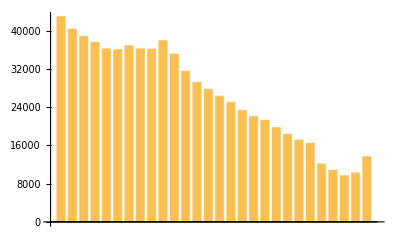

```mathematica
BarChart[bdpslo]
```

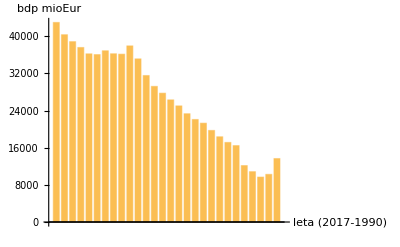

```mathematica
Show[%22,AxesLabel->{HoldForm[leta (2017-1990)],HoldForm[bdp mioEur]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

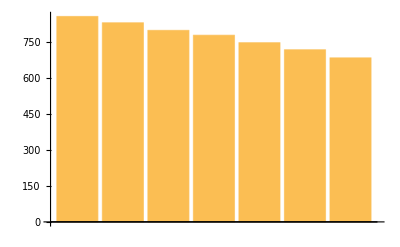

First::normal: Nonatomic expression expected at position 1 in First[].

```mathematica
BarChart[bdpnem]
```